```mathematica
(*http://reference.wolfram.com/language/tutorial/SolvingLinearSystems.zh.html*)
LinearSolve[{{1,2},{4,5}},{3,6}]
```

{-1,2}

```mathematica
p = {1,4};
q = {2,5};
```

```mathematica
p2=p * (-1)
```

{-1,-4}

```mathematica
q2=q * 2
```

{4,10}

```mathematica
v = p2 + q2
```

{3,6}

```mathematica
vectorGraphics[p_]:=Graphics[{Arrowheads[.07],Thickness[.01],Black,Arrow[{{0,0},p}]}]
```

```mathematica
g=vectorGraphics@p2;
```

```mathematica
g2=vectorGraphics@q2;
```

```mathematica
g3=vectorGraphics@v;
```

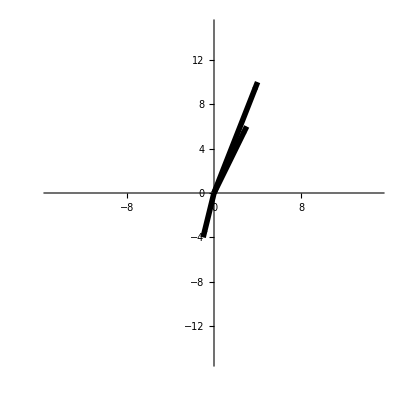

```mathematica
Show[g,g2,g3,PlotRange-> {{-15,15},{-15,15}},Axes-> True,AxesOrigin-> {0,0}]
```